```mathematica
f[x_]:= x^2
f[{1,2,3}]
```

{1,4,9}

```mathematica
ff[x_Integer]:=x^3
ff[4]
```

64

```mathematica
ff[4.]
```

ff[4.]

```mathematica
ff[x_Real]:=x^4
ff[4.]
```

256.



```mathematica
256.
Plot[x^2,{x, -2, 2}]
```

```mathematica
Clear["Global'*"]
```

```mathematica
f[x_Real]:=x^2
```

```mathematica
ff[x_]:=x^2
f[2]
```

4

```mathematica
f[2.0]
```

4.

```mathematica
ff[2]
```

8

```mathematica
ff[2.0]
```

16.

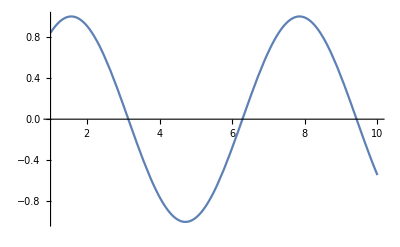

```mathematica
Plot[Sin[x],{x,1,10}]
```

```mathematica
f[Out[19]]
```

-Graphics-^2

```mathematica
y=4; a=3;
g[y_]:=y^2;
gg[y_]=y^2;
ggg[u_]=u^2;

g[3]
gg[3]
ggg[3]
```

9

16

9

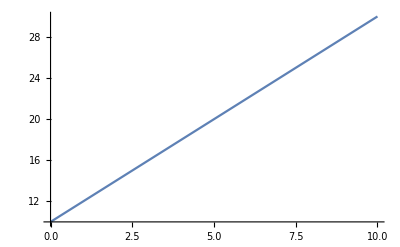

```mathematica
func[x_]:=2*x+10
Plot[func[x],{x, 0,10}]
```

```mathematica
Manipulate[Plot[Sin[x+a],{x, 0, 6Pi}],{a,0,6}]
```



```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}]
```

```mathematica
Manipulate[Plot[Sin[b*x+a],{x, -4, 4}],{{a,0,"Phase"},0,5}, {{b,1,"Frequency"},0,2}]
```

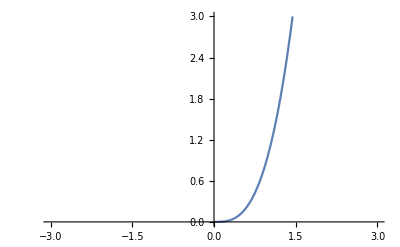

```mathematica
Plot[x^3,{x,-3,3},PlotRange->{{0,3}}]
```

```mathematica
func2[r_,ϕ_]:=r*Cos[ϕ];
func3[r_,ϕ_]:=r*Sin[ϕ];
r=1;
ParametricPlot[{func2[r,ϕ],func3[r,ϕ]},{ϕ,0,2 *Pi}]
```

-Graphics-

```mathematica
Manipulate[ParametricPlot[{func2[r1,ϕ],func3[r2,ϕ]},{ϕ,0,2 *Pi}],{r1,-10,10},{r2,-10,10}]
```

```mathematica
(*Происходит изменение радусов эллипса, причем при изменении r при косинусе график сжимается с боков, а при изменении при синусе - с полюсов, при одинаковых значениях r при косинусе и синусе график выглядит как окружность*)
```

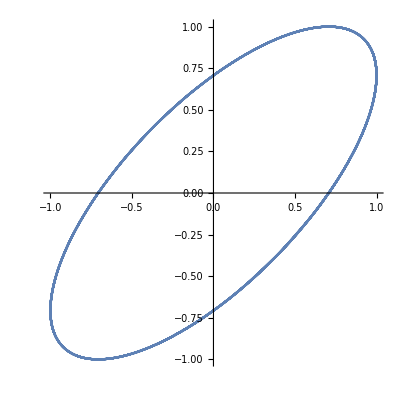

```mathematica
n=2;
δ=(n-1)*π/(n*2);
xt[t_]:=Sin[2*t+δ];
yt[t_]:=Sin[2*t];
ParametricPlot[{xt[t],yt[t]},{t,-10,10}]
```

```mathematica
(*Manipulate[ParametricPlot[{Sin[2*t+δ],yt[t]},{t,-10,10}],{δ,0,2Pi}]
```

```mathematica
*)
(*При изменении дельты происходит сжатие графика: при дельта =0 график представляет собой прямую, при дельта = π/4 график выглядит как окружность,при дельта от 0 до π/2 он расширяется в направлении y=-x и сжимается по направлению y=x, далее наоборот, график меняется периодически с периодом 2π*)

xt5[a_,t_]:=Sin[a*t+δ];

yt5[b_,t_]:=Sin[b*t];
Manipulate[ParametricPlot[{xt5[a,t],yt5[b,t]},{t,0,50}}],
{{a,0,"Variable a"},-10,10},{{b,0,"Variable b"},-10,10}]
```

```mathematica
xt5[a_,t_]:=Sin[a*t+δ];
```

```mathematica
yt5[b_,t_]:=Sin[b*t];
```

```mathematica
Manipulate[ParametricPlot[{xt5[a,t],yt5[b,t]},{t,0,50}}],
{{a,0,"Variable a"},-10,10},{{b,0,"Variable b"},-10,10}]
```

```mathematica
xt5[an_,tn_]:=Sin[an*tn+δ]
```

```mathematica
yt5[bn_,tn_]:=Sin[bn*tn]
```

```mathematica
Manipulate[ParametricPlot[{xt5[an,tn],yt5[bn,tn]},{tn,0,50}}],
{{an,0,"Variable a"},-10,10},{{bn,0,"Variable b"},-10,10}]
```

```mathematica
Manipulate[ParametricPlot[{xt5[an,tn],yt5[bn,tn]},{tn,0,50}],{{an,0},-10,10},{{bn,0},-10,10}]
```

```mathematica
list1={1,2,3,6,8,10}
```

{1,2,3,6,8,10}

```mathematica
lst1=Join[list1,{6,7,8}]
```

{1,2,3,6,8,10,6,7,8}

```mathematica
ListPlot[lst1]
```

ListPlot::lpn: lst1 is not a list of numbers or pairs of numbers.

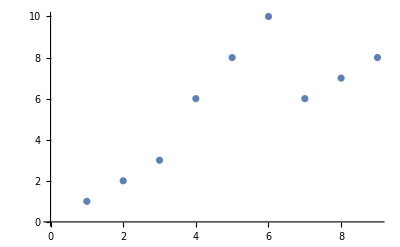

```mathematica
ListPlot[lst1]
```

```mathematica
ListPlot[lst1]
```

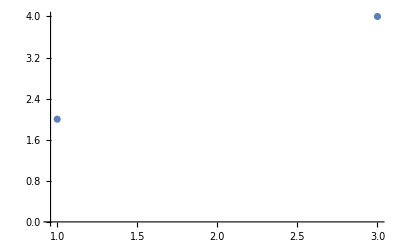

```mathematica
ListPlot[{{1,2},{3,4}}]
```

```mathematica
VectorQ[lst1]
```

True

```mathematica
m={{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
a =MatrixForm[m]
```

(1 | 2
3 | 4)

```mathematica
5*a
```

```mathematica
5 ({{1, 2}, {3, 4}})
Det[m]
```

{{5,10},{15,20}}

-2

```mathematica
Inverse[m]
```

{{-2,1},{3/2,-1/2}}

```mathematica
MatrixForm[Transpose[m]]
```

(1 | 3
2 | 4)

```mathematica
TensorRank[m]
```

2

```mathematica
a1={1,2,3}
a2={3,4,5}
```

{1,2,3}

{3,4,5}

```mathematica
a1*a2
```

{3,8,15}

```mathematica
Dot[a1,a2]
```

26

```mathematica
a1.a2
```

26